# Projektövning - problemlösning i Mathematica

(Rapportskalet använder sig av ett stylesheet tillverkat av Göran Andersson)

Stefan Sarkis, Evan Saboo

## 1. Introduktion: problemformulering

### 1.1 Sammanfattning av uppgifter

#### 3.2

a)
I första deluppgiften ska man lösa ut och plotta differentialekvationen c’(t) = t^2 c^3 med begynnelsevillkoret  c(1) = p, där p är en av gruppens födelsedag ( mellan 1 och 31). Sedan ska man få ut alla värden på t i lösningen. 
För att lösa deluppgiften använde vi  först datatypen DSolve för att lösa ut differentialekvationen med begynnelsevillkoret och plottade lösningen i en lämplig intervall. Sedan tog vi en del av lösningen och använde oss av Solve för att lösa ut alla värden på t i lösningsgrenen.

b) 
I den andra deluppgiften ska man lösa ut samma differentialekvation med samma begynnelsevillkor utan Mathematica (alltså med hanskrivning) och sedan ska man kontrolera om lösningen är korrekt.
Eftersom ekvationen är separabel så kunde vi lösa ut lösningrenen utan större problem och vi kontrollerade att lösningen stämmde med Mathematicas lösning.

c)
I den sista deluppgiften ska man formulera ett nytt randvillkor så att man får den andra lösningsgrenen i differantialekvationen  c’(t) = t^2 c^3 och sedan ska man få ut alla t i lösningsgrenen efter att man har plottat den.
Vi använde oss igen av DSolve utan något begynnelsevillkor för att få ut lösningsgrenarna i differntialekvationen. Vi formulerade sedan ut ett nytt begynnelsevillkor och använde DSolve för att bara få ut den andra lösningsgrenen och plottade den i en lämplig intervall.
till sist gorde samma sak som i den första delfrågan för att lösa ut alla värden på t.

### 1.2 Sammanfattning del 2

## 2 Genomförande och härledningar

### 2.1 Uppgift 3.1)

#### a)

```mathematica
p:= 20
```

```mathematica
f[x_]:=Sqrt[(p*x^2)+x^4]
```

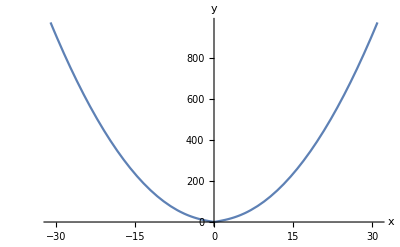

```mathematica
Plot[f[x],{x,-31,31},AxesLabel->{x,y}]
```

#### b)

```mathematica
x1:=-1
```

```mathematica
x2:=2
```

```mathematica
Integrate[f[x],{x,x1,x2}]
```

-(80 √5)/3+16 √6+7 √21

```mathematica
NIntegrate[f[x],{x,x1,x2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

11.6414

#### c)

```mathematica
F[x_]=Integrate[f[x],x]
```

((x^2 (20+x^2))^(3/2))/(3 x^3)

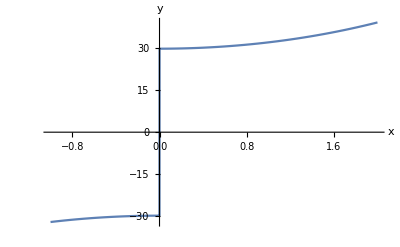

```mathematica
Plot[F[x],{x,x1,x2},AxesLabel->{x,y}]
```

```mathematica
Limit[F[x],x->0,Direction->-1]
```

(40 √5)/3

```mathematica
Limit[F[x],x->0,Direction->1]
```

-(40 √5)/3

#### d)

```mathematica
F[x2]-F[x1]
```

16 √6+7 √21

#### e)

```mathematica
Integrate[f[x],{x,-1,1}]+Integrate[f[x],{x,1,2}]
```

-(80 √5)/3+16 √6+7 √21

```mathematica
x3:=1
```

```mathematica
(F[x3]-F[x1])+(F[x2]-F[x3])
```

16 √6+7 √21

#### f)

-Graphics-

### 2.2 Uppgift 3.2)

#### a)

Först rensar vi alla globala variablar från dess värden, sedan använder vi dataypen DSolve för att lösa ut  differentialekvationen c’(t) = t^2 c^3 med begynnesevilkoret  c(1) = p där vi har deffinerat p som 20 för att begynnelsevilkoret ska gälla.

```mathematica
ClearAll["`*"]
```

```mathematica
p :=20
```

```mathematica
sol=DSolve[{ c'[t]==t^2*c[t]^3,c[1]==p},c[t], t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{c[t]→(20 √3)/(√(803-800 t^3))}}

Efter att vi fick ut lösningen plottar vi det i en lämplig intervall och markerar begynnelsevilkoret p(1)=20.

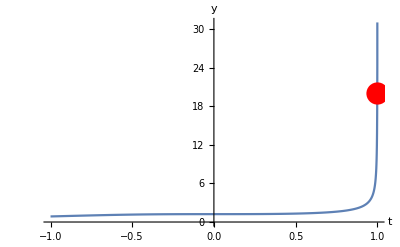

```mathematica
Plot[c[t]/.sol,{t,-1,2},AxesLabel->{t,y},PlotRange->{0,31},Epilog->{PointSize[.04], Red,Point[{1,p}]}]
```

I sista delen av uppgiften använder vi datatypen Solve för att lösa ut alla t vår lösning gäller för.

```mathematica
Solve[Sqrt[803-800 t^3]==0]
```

{{t→-(-803)^(1/3)/(2 10^(2/3))},{t→803^(1/3)/(2 10^(2/3))},{t→((-1)^(2/3) 803^(1/3))/(2 10^(2/3))}}

Vi har fått ut fått ut 3 olika t som vår lsöning gäller för.

#### b)

I den andra deluppgiften löser vi ut differentialekvationen för hand. Eftersom vi vet att ekvationen är en separabel differentialekvation så kan vi lösa den med ett enkelt metod.
-Graphics-

Efter att vi fick ut lösningen med hand plottar vi det i ett lämpligt intervall.

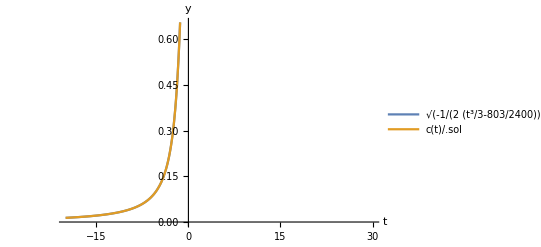

```mathematica
Plot[{Sqrt[-(1/2)/(((t^3)/3)-(803/2400))],c[t]/.sol},{t,-20,30},AxesLabel-> {t,y},  PlotLegends->"Expressions"]
```

Vi plottar också ut Mathematicas lösning i samma för att kunna jämföra den med den handskrivna lösningen.

#### c)

I sista deluppgiften ska vi plotta ut den andra lösningen till differntiaekvationen c’(t) = t^2 c^3. Första löser vi ut båda lösnngarna till ekvationen utan begynnelsevilkoret p(0)=20 genom DSolve.

```mathematica
ClearAll["`*"]
```

```mathematica
sol=DSolve[ c'[t]==t^2*c[t]^3,c[t], t]
```

{{c[t]→-(√(3/2))/(√(-t^3-3 C[1]))},{c[t]→(√(3/2))/(√(-t^3-3 C[1]))}}

Genom DSolve ser vi att den första lösningen är en negativ ekvation. Genom att sätta begynnelsevilkoret p som -20 så kan vi få ut den odefinerade konstanten C[1] med den negativa lösningen. Vi plottar sedan ut den negativa lösningen i intervallet [-1,2].

```mathematica
p:=-20;
```

```mathematica
sol=DSolve[{ c'[t]==t^2*c[t]^3,c[1]==p},c[t], t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{c[t]→-(20 √3)/(√(803-800 t^3))}}

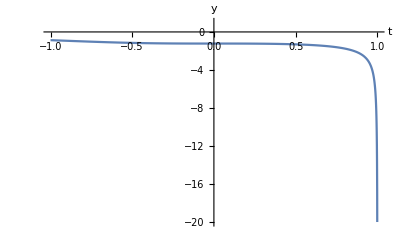

```mathematica
Plot[c[t]/.sol, {t, -1,2}, AxesLabel->{t,y}, PlotRange->{p,1}]
```

Vi använder Solve för att få ut alla värden på t i den negativa lösningen.

```mathematica
Solve[(-Sqrt[803-800 t^3])==0]
```

{{t→-(-803)^(1/3)/(2 10^(2/3))},{t→803^(1/3)/(2 10^(2/3))},{t→((-1)^(2/3) 803^(1/3))/(2 10^(2/3))}}

## 3. Resultat, diskussion och slutsats

### Uppgift 3.1

### Uppgift 3.2

#### a)

I första deluppgiften fick vi en lösning på differentialekvationen c’(t) = t^2 c^3 med begynnesevilkoret  c(1) = 20 med hjälp av datatypen DSolve. Lösningen är:(20 √3)/(√(803-800 t^3)).
-Graphics-

Grafen visar lösningen till differentialekvationen med den markerade punkten p(1)=20, där t=1 och y = 20.

För att få ut vilka t vår lösning gäller så använde vi datatypen Solve och fick ut tre t eftersom lösnnigen är tredjegradsekvation:

{{t→-(-803)^(1/3)/(2 10^(2/3))},{t→803^(1/3)/(2 10^(2/3))},{t→((-1)^(2/3) 803^(1/3))/(2 10^(2/3))}}

#### b)

Vi löste ut differentialekvationen c’(t) = t^2 c^3 med begynnesevilkoret  c(1) = 20 utan Mathematica och fick lösningen: Sqrt[-0.5/(((t^3)/3)].
Vi kan bevisa att lösningen stämmer med Mathematicas lösning genom 2 metoder.

1. Den första metoden går ut på att plotta den handskrivna- och Mathematica lösningen i samma graf.
-Graphics-

Vi kan se i grafen att linjerna är identiska med varandra och då kan komma fram till att lösningarna är likadana.

2. I den andra metoden ska vi sätta in pröva att sätta in t=1 i den handrskrivna lösningen.

```mathematica
ClearAll["`*"]
```

```mathematica
c[t_]=Sqrt[-(1/2)/(((t^3)/3)-(803/2400))]
```

(√(-1/(-803/2400+t^3/3)))/(√2)

```mathematica
c[1]
```

20

Då får svaret 20 som stämmer med begynnelsevilkoret p(1)=20. och vi kan komma fram till att ekvationen (lösningen) stämmer med Mathematica.

#### c)

I den sista deluppgiften ska vi få ut den andra lösningsgrenen genom att först andävnda dataypen DSolve för att lösa ut diffentialekvationen  c’(t) = t^2 c^3 utan randvilkor.
Vi får ut dessa lösningar: {{c[t]→-(√(3/2))/(√(-t^3-3 C[1]))},{c[t]→(√(3/2))/(√(-t^3-3 C[1]))}}.
Vi ser att den andra lösningsgrenen är negativ så vi använder avänder DSolve  begynnelsevillkoret p(1)=-20  för att bara få ut den negativa lösningsgrenen.
 -Graphics-
 Här har vi plottat ut den andra lösningsgrenen i en lämplig intervall.
 


För att få ut vilka t vår andra lösningsgren gäller så använde vi datatypen Solve och fick ut tre t eftersom lösnnigen är tredjegradspolynom:

{{t→-(-803)^(1/3)/(2 10^(2/3))},{t→803^(1/3)/(2 10^(2/3))},{t→((-1)^(2/3) 803^(1/3))/(2 10^(2/3))}}